## Harmonicity Measurement

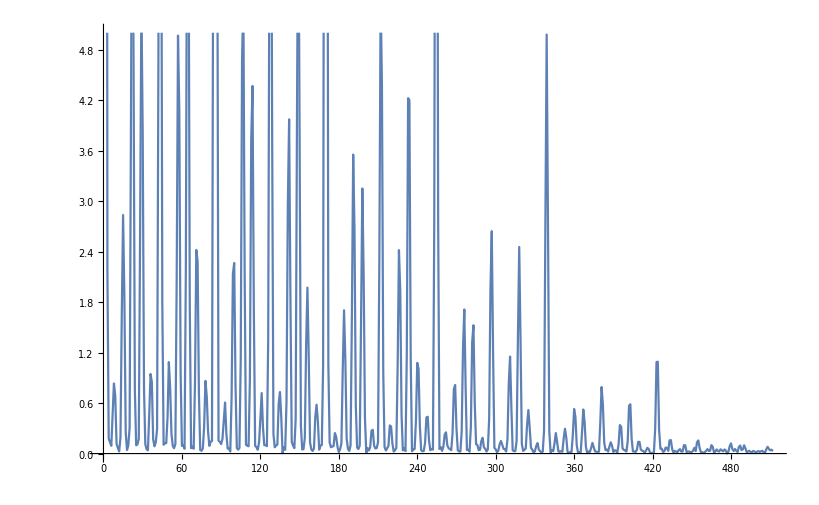

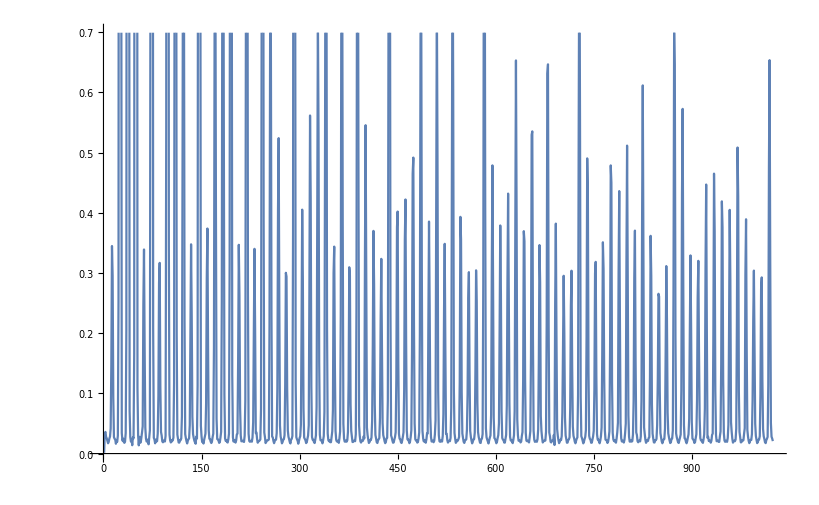

0.155472

0.272794

```mathematica
input1Length = 2^11;
saw[t_]:=2SawtoothWave[t]-1
input1 = Table[saw[24.232N[t]/input1Length],{t,1,input1Length}];
input1 += Table[saw[24.232*(3/2)N[t]/input1Length],{t,1,input1Length}];
input1 += Table[saw[24.232*(4/2)N[t]/input1Length],{t,1,input1Length}];
ListLinePlot[input1];
window[length_]:=Table[BlackmanWindow[t/(length)],{t,-length/2,length/2-1}];
spectrum[x_]:=Abs[Take[Fourier[window[Length[x]]*x],Length[x]/2]]
spectrumNoWindow[x_]:=Abs[Take[Fourier[x],Length[x]/2]]
spectrum1 = spectrum[input1];
toDecibels[X_]:=Log10[X/20];
fromDecibels[x_]:=20 10^(x)
logSpectrum1 = toDecibels[spectrum1];
cepstrum[x_]:=Identity[spectrum[Identity[spectrum[x]]]]
ListLinePlot[cepstrum[input1]/Mean[cepstrum[input1]],PlotRange->{0,5}]
ListLinePlot[spectrum[input1]]
SFM[X_]:=GeometricMean[X]/Mean[X]
SFM[cepstrum[input1]]
SFM[spectrum[input1]]
```

```mathematica
Solve[vnd1Length + vnd1Length/taps + vnd1Length/taps^2 == totalLength,vnd1Length]
```

```mathematica
{{vnd1Length->(taps^2 totalLength)/(1+taps+taps^2)}}/.{totalLength->1,taps->16}
```

{{vnd1Length→256/273}}

```mathematica
48000/256//N
```

187.5

```mathematica
10^(60/20)
```

1000